```mathematica
map={{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,0,0,0,0,0,1,1,1,0,0,0,1},{8,0,0,0,0,0,0,0,1,1,1,0,0,0,1},{1,0,0,0,1,1,1,0,0,1,0,0,0,0,1},{1,0,0,0,1,1,1,0,0,0,0,0,1,0,1},{1,1,0,0,1,1,1,0,0,0,0,0,1,0,1},{1,0,0,0,0,1,0,0,0,0,1,1,1,0,1},{1,0,1,1,0,0,0,1,0,0,0,0,0,0,5},{1,0,1,1,0,0,0,1,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}};
```

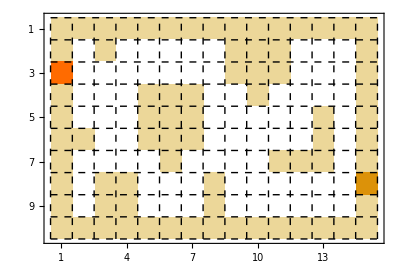

/Users/xiaotingtang/Dropbox/Interests/Mathematica派/MathematicaPi

geneticDemo1_0.png

```mathematica
g=MatrixPlot[map,FrameTicks->{Range[10],Range[15]},Mesh->All,MeshStyle->{Dashed},ColorRules->{2->Green,3->Black}]
SetDirectory@NotebookDirectory[]
Export["geneticDemo1_0.png",g]
```

```mathematica
Grid[Transpose[{{"上","下","左","右"},{0,1,2,3},{00,01,10,11}}],Frame->All]
```

上 | 0 | 0
下 | 1 | 1
左 | 2 | 10
右 | 3 | 11

```mathematica
RandomChoice[{"00","01","10","11"},20]
```

{00,00,00,01,00,00,10,10,01,11,00,01,10,01,01,00,00,00,01,10}

```mathematica
map={{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,1,0,0,0,0,0,1,1,1,0,0,0,1},{8,0,0,0,0,0,0,0,1,1,1,0,0,0,1},{1,0,0,0,1,1,1,0,0,1,0,0,0,0,1},{1,0,0,0,1,1,1,0,0,0,0,0,1,0,1},{1,1,0,0,1,1,1,0,0,0,0,0,1,0,1},{1,0,0,0,0,1,0,0,0,0,1,1,1,0,1},{1,0,1,1,0,0,0,1,0,0,0,0,0,0,5},{1,0,1,1,0,0,0,1,0,0,0,0,0,0,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}};
```